# Using the SACNA package - APED model

The purpose of this document is to give a short tutorial for the SACNA package. 
Let’s start by bringing the package functions to this notebook.

```mathematica
Quiet[ClearAll["Global`*"]];
 Quiet[Remove["Global`*"]];
SetDirectory[NotebookDirectory[]];

Quiet[Get["../SACNA.wl"]]
```

Now let’s input the reactions and rates lists of this model. If we input the rates list as an empty list, SACNA will assign rates by default in the order of the list (the first reaction has constant k1 and so on). Reactions must be in terms of D-species, L-species, Z-species (achiral species), and the empty specie N1.

```mathematica
reactions = {"L1->L2","L2->L1","L2+L1->L3","D2+L1->D4","L3->2L1","L4->L1+D1","L4->D3","D3->L4"};
rates={};
```

Note that we are not writing all the reactions, only it is left the dual reactions. If we use the function ClausuraDual, we can get all the reactions. This is done by default in the RunSemiAlgebraicAnalysis function.

```mathematica
Quiet[ClausuraDual[reactions]]
```

{L1->L2,L2->L1,L1+L2->L3,D2+L1->D4,L3->2L1,L4->D1+L1,L4->D3,D3->L4,D1->D2,D2->D1,D1+D2->D3,D1+L2->L4,D3->2D1,D4->D1+L1,D4->L3,L3->D4}

Now we can run the semialgebraic analysis of the model by using the RunSemiAlgebraicAnalysis function. The first parameter corresponds to the reactions’ list, the second parameter corresponds to the rates’ list, and the last parameter corresponds to time in seconds (the Collins’ algorithm may take so much time to find a solution). The function will ask for the Routh-Hurwitz condition number. Considering the first and last numbers will be faster, because this conditions are shorter than the others.  This example give us 4 Routh-Hurwitz conditions. Let’s begin with the first condition.

```mathematica
time=60;
cadSolutions=RunSemiAlgebraicAnalysis[reactions,rates,time]
```

False

The first condition cannot be satisfied. As mentioned before, let’s try with the last condition (in this case, the fourth one).

```mathematica
time=60;
cadSolutions=RunSemiAlgebraicAnalysis[reactions,rates,time]
```

D1>0&&D2>0&&D3>0&&D4>0&&k1>0&&0<k2<(D1 k1)/D2&&(D1 k1-D2 k2)/(2 D1 D2)<k3<(D1 k1-D2 k2)/(D1 D2)&&k4==(D1 k1-D2 k2-D1 D2 k3)/(D1 D2)&&(((D1 D2 k3)/D3<k5<(D1^2 k1^2 k3-D2^2 k2^2 k3+D1^2 D2 k1 k3^2+D1 D2^2 k2 k3^2+3 D1^2 D2 k1 k3 k4-D1 D2^2 k2 k3 k4+2 D1^2 D2^2 k3^2 k4+2 D1^2 D2^2 k3 k4^2)/(2 D1 D3 k1 k3+2 D2 D3 k2 k3-2 D1 D3 k1 k4+2 D2 D3 k2 k4+8 D1 D2 D3 k3 k4)&&k6==(D1 k1-D2 k2+D1 D2 k3+D1 D2 k4-2 D3 k5)/(2 D4)&&(-D1 D2 k3+D3 k5)/D4<k7<(-D1^2 D2 k1 k3^2 k6-D1 D2^2 k2 k3^2 k6-2 D1^2 D2^2 k3^2 k4 k6+D1 D3 k1 k3 k5 k6+D2 D3 k2 k3 k5 k6+2 D1 D2 D3 k3 k4 k5 k6)/(D1 D3 k1 k4 k5-D2 D3 k2 k4 k5-2 D1 D2 D3 k3 k4 k5+D1 D4 k1 k3 k6+D2 D4 k2 k3 k6+2 D1 D2 D4 k3 k4 k6)&&k8==(D1 D2 k3-D3 k5+D4 k7)/D3)||((D1^2 k1^2 k3-D2^2 k2^2 k3+D1^2 D2 k1 k3^2+D1 D2^2 k2 k3^2+3 D1^2 D2 k1 k3 k4-D1 D2^2 k2 k3 k4+2 D1^2 D2^2 k3^2 k4+2 D1^2 D2^2 k3 k4^2)/(2 D1 D3 k1 k3+2 D2 D3 k2 k3-2 D1 D3 k1 k4+2 D2 D3 k2 k4+8 D1 D2 D3 k3 k4)≤k5<(D1 k1-D2 k2+D1 D2 k3+D1 D2 k4)/(2 D3)&&k6==(D1 k1-D2 k2+D1 D2 k3+D1 D2 k4-2 D3 k5)/(2 D4)&&k7>(-D1 D2 k3+D3 k5)/D4&&k8==(D1 D2 k3-D3 k5+D4 k7)/D3))

As the algorithm found a solution, let’s find some particular solutions by using the FindInstance command.  Note that the solution doesn’t contain an expression for the L-species. It’s because we are assuming the racemic condition.

```mathematica
numberOfSamples=10; (*feel free to change*)
samplesList=FindInstance[cadSolutions,DeleteCases[DeleteDuplicates@Cases[cadSolutions,_Symbol,Infinity], Alternatives@@{GreaterEqual,Greater,Less,LessEqual}],numberOfSamples];
sampleNumber=8;   (*feel free to change*)
samplesList[[sampleNumber]]
```

{D1→516,D2→24,D3→77,D4→95,k1→89,k2→32,k3→179/56,k4→1625/3612,k5→3197952300132/5904530219,k6→582361127400/16026582023,k7→72,k8→27872957793960/454648826863}

Now we are ready to using the SACNA’s system simulator with the  ReactionSystemSimulator function. The simulation time depends on the sample. The user has to set it up.

Species Concentrations Graphic

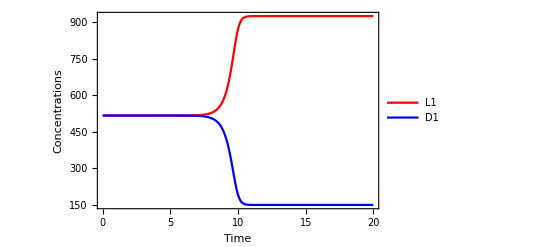

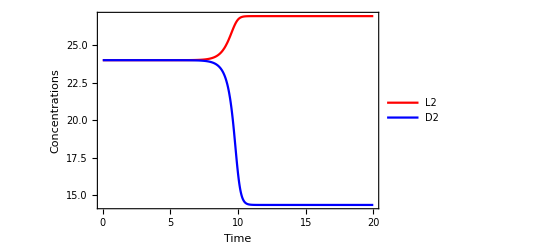

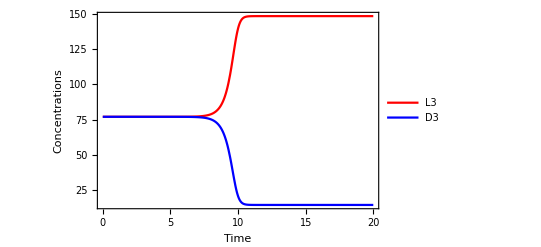

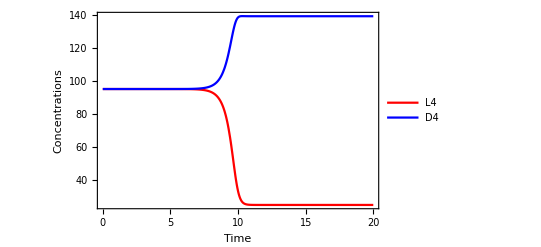

```mathematica
simulationTimeMin=0; 
simulationTimeMax=20; (*feel free to change*)
graficss=ReactionSystemSimulator[reactions,rates, samplesList[[sampleNumber]],0.000001,t,simulationTimeMin,simulationTimeMax];
```

SACNA also allows to export a simulation results to ChemKinLator simulator files with the function ExportToChemKinLator.

```mathematica
content=ExportToChemKinLator[reactions,rates, samplesList[[sampleNumber]],1/1000000000000000,1/1000000000000000,0,simulationTimeMax,1000];
```

Export::chtype: First argument $Canceled is not a valid file specification.

We could try to do the same with the second and third Routh-Hurwitz condition, but in this case it could take a lot of time.

The user would like to know which rate constant corresponds to some reactions. It can be done with the function GetReactionsAndRates.

```mathematica
GetReactionsAndRates[reactions,rates] //MatrixForm
```

(L1->L2 | k1
L2->L1 | k2
L1+L2->L3 | k3
D2+L1->D4 | k4
L3->2L1 | k5
L4->D1+L1 | k6
L4->D3 | k7
D3->L4 | k8
D1->D2 | k1
D2->D1 | k2
D1+D2->D3 | k3
D1+L2->L4 | k4
D3->2D1 | k5
D4->D1+L1 | k6
D4->L3 | k7
L3->D4 | k8)